NB: Sending χ→-χ to flip plot the right way round

ω_s<<ω_FSR?: ω_s=37500., ω_FSR=7500

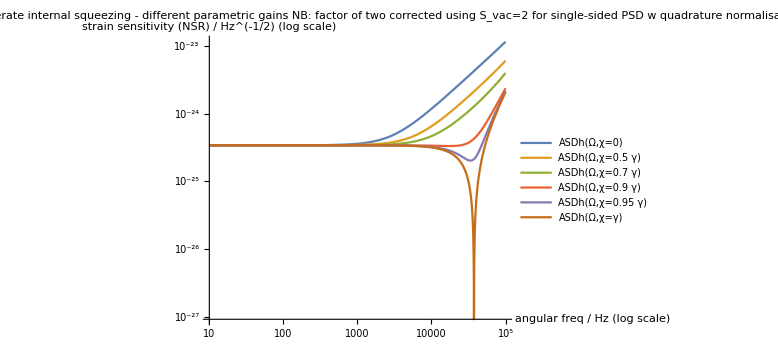

```mathematica
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
(*Using the same values as Fig.3 in Korobko et al, 2019: benchmark 3rd generation detector*)
λ=1550 10^-9(*m*);
w0=2π c/λ;
P = 4 10^6(*W*);
Larm=20 10^3(*m*);
Lse=56(*m*);
Titm=0.07;
Tse=0.35;
ws=c(Titm/(4 Lse Larm))^(1/2);
Print[StringForm["ω_s<<ω_FSR?: ω_s=``, ω_FSR=``",ws,c/(2 Larm)]]
γ=(c Tse)/(4 Lse); (*later called kout*)
(*the authors don't say what value they use for χ, threshold?*)
Sh[Ω_,χ_]:=(ℏ c)/(8 P Larm w0)(Ω^2(γ-χ)^2+(ws^2-Ω^2)^2)/(ws^2 γ)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
LogLogPlot[{ASDh[Ω,χ=0],ASDh[Ω,χ=0.5γ],ASDh[Ω,χ=0.7γ],ASDh[Ω,χ=0.9γ],ASDh[Ω,χ=0.95γ],ASDh[Ω,χ=γ]},{Ω,10,10^5},AxesLabel->{"angular freq / Hz (log scale)", "strain sensitivity (NSR) / Hz^(-1/2) (log scale)"},ImageSize->Large,PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless degenerate internal squeezing - different parametric gains\nNB: factor of two corrected using S_vac=2 for single-sided PSD w quadrature normalisation"]
```

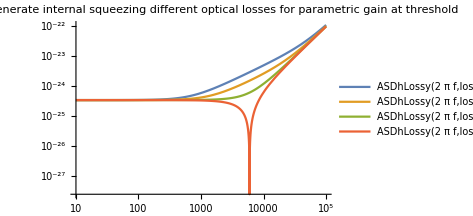
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^(-1/2) (log scale)

```mathematica
(*Lossy result*)
χ=γ;(*at threshold*)
kout=γ;
(*lossRatio=kloss/(kloss+kout),(kout*loss)/(1-loss)=kloss*)
(*have omitted factor 1/2 since it should have cancelled with quadrature normalisation in Subscript[S, vac]*)
ShLossy[Ω_,lossRatio_]:=(ℏ c)/(8 P Larm w0)(Ω^2((kout+(kout*lossRatio)/(1-lossRatio)+χ)^2-4kout χ)+(ws^2-Ω^2)^2)/(ws^2 kout)
ASDhLossy[Ω_,lossRatio_]:=Abs[ShLossy[Ω,lossRatio]]^(1/2)
Labeled[LogLogPlot[{
ASDhLossy[2π f,lossRatio=0.1],
ASDhLossy[2π f,lossRatio=0.03],
ASDhLossy[2π f,lossRatio=0.005],
ASDhLossy[2π f,lossRatio=0]},{f,10,10^5},ImageSize->350,PlotRange->All,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nfor parametric gain at threshold"],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
Clear[χ]
```

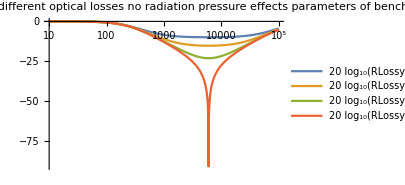
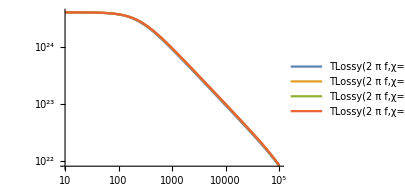
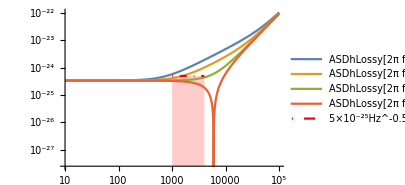
-Graphics-shot noise transfer function,
|R| / dB (20log10)
-Graphics-signal transfer function,
|T| / [?] (log scale)
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^-0.5 (log scale)

```mathematica
(*plotting |T| and (|R1|^2+|R2|^2)^(1/2)*)
Clear[χ]
G=((2P Larm w0)/(ℏ c))^(1/2);
TLossy[Ω_,χ_,lossRatio_]:=Abs[(2I ws G (2 kout)^(1/2))/(Ω(kout+(kout*lossRatio)/(1-lossRatio)+χ)+I(ws^2-Ω^2))]
(*Already calculated |R1|^2+|R2|^2 manually, see Subscript[S, Subscript[X, 1],out](Ω)*)
RLossy[Ω_,χ_,lossRatio_]:=(1-(4 Ω^2 kout χ)/(Ω^2(kout+(kout*lossRatio)/(1-lossRatio)+χ)^2+(ws^2-Ω^2)^2))^(1/2)
p1=Labeled[LogLinearPlot[{
20Log10[RLossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0]]},{f,10,10^5},ImageSize->300,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector",
ImagePadding->{{45,10},{0,0}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^5},All}],"shot noise transfer function,\n|R| / dB (20log10)",Left,RotateLabel->True,LabelStyle->Directive[10]];
p2=Labeled[LogLogPlot[{
TLossy[2π f,χ=kout,lossRatio=0.1],
TLossy[2π f,χ=kout,lossRatio=0.03],
TLossy[2π f,χ=kout,lossRatio=0.005],
TLossy[2π f,χ=kout,lossRatio=0]},{f,10,10^5},ImageSize->300,PlotRange->{{10,10^5},All},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],
ImagePadding->{{45,10},{0,5}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],}],"signal transfer function,\n|T| / [?] (log scale)",Left,RotateLabel->True,LabelStyle->Directive[10]];
χ=kout;
p3=Labeled[LogLogPlot[{
ASDhLossy[2π f,lossRatio=0.1],
ASDhLossy[2π f,lossRatio=0.03],
ASDhLossy[2π f,lossRatio=0.005],
ASDhLossy[2π f,lossRatio=0],
If[10^3<#<4 10^3,5 10^-25,Null]&[f]},{f,10,10^5},ImageSize->300,PlotRange->{{10,10^5},All},PlotLegends->LineLegend[{"ASDhLossy[2π f,lossRatio=0.1]","ASDhLossy[2π f,lossRatio=0.03]","ASDhLossy[2π f,lossRatio=0.005]","ASDhLossy[2π f,lossRatio=0]","5×10^-25Hz^-0.5 target for 1–4 kHz"},LabelStyle->Directive[10]],
ImagePadding->{{45,10},{10,5}},Filling->{5->Bottom},PlotStyle->{,,,,Directive[DotDashed,Red]}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]];
Column[{p1,p2,p3},Spacings->0]
```

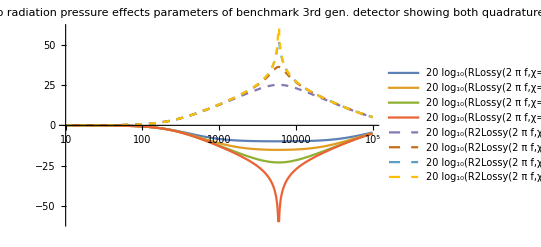
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^-0.5 (log scale)

```mathematica
(*checking other quadrature, noise transfer function is the same as before, just with χ->-χ*)

R2Lossy[Ω_,χ_,lossRatio_]:=(1+(4 Ω^2 kout χ)/(Ω^2(kout+(kout*lossRatio)/(1-lossRatio)-χ)^2+(ws^2-Ω^2)^2))^(1/2)
Labeled[LogLinearPlot[{
20Log10[RLossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[RLossy[2π f,χ=kout,lossRatio=0]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.1]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.03]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0.005]],
20Log10[R2Lossy[2π f,χ=kout,lossRatio=0]]},{f,10,10^5},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector\nshowing both quadratures\nsee that optical loss affects the squeezed quadrature more,\njust like a degenerate OPO",PlotStyle->{,,,,Dashed,Dashed,Dashed,Dashed},PlotRange->{{10,10^5},{-60,60}}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

```mathematica
(*to-do: plotting the same as above, but for the LIGO Voyager parameters used by Li et al, 2020 for direct comparison to those plots + conventional detector*)
```

```mathematica
(*stability of degenerate internal squeezing*)
Clear[χ,lossRatio]
ktot[lossRatio_]:=kout+(kout*lossRatio)/(1-lossRatio);
poles[χ_,lossRatio_]:={(-I (ktot[lossRatio]+χ)+(-(ktot[lossRatio]+χ)^2+4 ws^2)^(1/2))/2,(-I (ktot[lossRatio]+χ)-(-(ktot[lossRatio]+χ)^2+4 ws^2)^(1/2))/2};
Manipulate[ListPlot[{
{Re[poles[χ,lossRatio][[1]]],Im[poles[χ,lossRatio][[1]]]},
{Re[poles[χ,lossRatio][[2]]],Im[poles[χ,lossRatio][[2]]]}},PlotRange->{-10^6,10^5},AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium],PlotLabel->StringForm["poles of lossy transfer function\nχ/kout=``, lossRatio=``",χ/kout,lossRatio]],{{χ,0},0,2kout},{{lossRatio,0},0,1}]
Manipulate[ListPlot[{
{Re[poles[χ,lossRatio][[1]]],Im[poles[χ,lossRatio][[1]]]},
{Re[poles[χ,lossRatio][[2]]],Im[poles[χ,lossRatio][[2]]]}},PlotRange->{-10^4,10^4},AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium],PlotLabel->StringForm["poles of lossy transfer function\nχ/kout=``, lossRatio=``",χ/kout,lossRatio]],{{χ,0},0,2kout},{{lossRatio,0},0,1}]
```

SetDelayed::write: Tag Real in 4.74342×10^7[lossRatio_] is Protected.

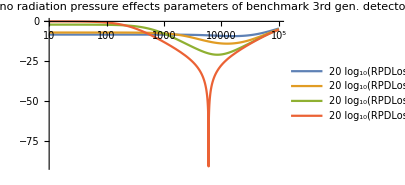
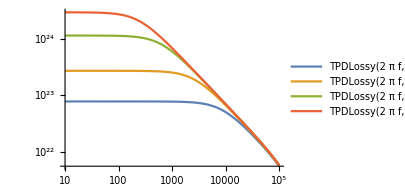
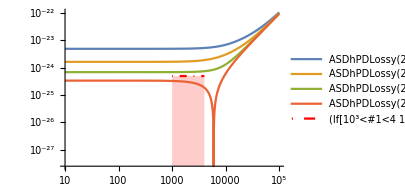
-Graphics-shot noise transfer function,
|R| / dB (20log10)
-Graphics-signal transfer function,
|T| / [?] (log scale)
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^-0.5 (log scale)

```mathematica
(*introducing intracavity loss in â mode (κa as opposed to κaqtot, κaqout) + photodetector (PD) loss, Subscript[R, PD] is the reflectivity of the lossless beam-splitter before the PD,
copying code from above*)
Clear[χ]
κa[lossRatio_]:=(kout*lossRatio)/(1-lossRatio);
κaq[lossRatio_]:=kout+(kout*lossRatio)/(1-lossRatio);
κaqout=kout;
TPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=(1-Rpd)^(1/2)Abs[(2 (κaqout)^(1/2)ws G)/((κaq[lossRatio]+χ-I Ω)(κa[lossRatio]-I Ω)+ws^2)]
RPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=((1-Rpd)(
Abs[(2κaqout-κaq[lossRatio]-χ+I Ω-ws^2/(κa[lossRatio]-I Ω))/(κaq[lossRatio]+χ-I Ω+ws^2/(κa[lossRatio]-I Ω))]^2
+Abs[(2(κaqout (κaq[lossRatio]-κaqout))^(1/2))/(κaq[lossRatio]+χ-I Ω+ws^2/(κa[lossRatio]-I Ω))]^2
+Abs[(2(κaqout κa[lossRatio])^(1/2)ws)/((κaq[lossRatio]+χ-I Ω)(κa[lossRatio]-I Ω)+ws^2)]^2)+Rpd)^(1/2)
ASDhPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=(1/(4 κaqout ws^2 G^2)(((2κaqout-κaq[lossRatio]-χ)κa[lossRatio]+Ω^2-ws^2)^2+Ω^2(κa[lossRatio]-(2κaqout-κaq[lossRatio]-χ))^2+4κaqout κa[lossRatio] ws^2+ (κa[lossRatio]^2+ Ω^2)(4κaqout (κaq[lossRatio]-κaqout)+Rpd/(1-Rpd) )))^(1/2)(*RPDLossy[Ω,χ,lossRatio,Rpd]/TPDLossy[Ω,χ,lossRatio,Rpd]*)
p1=Labeled[LogLinearPlot[{
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0]],
20Log10[RPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0]]},{f,10,10^5},ImageSize->300,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy degenerate internal squeezing\ndifferent optical losses\nno radiation pressure effects\nparameters of benchmark 3rd gen. detector\nnow with â mode intracavity loss and PD loss",
ImagePadding->{{45,10},{0,0}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^5},All}],"shot noise transfer function,\n|R| / dB (20log10)",Left,RotateLabel->True,LabelStyle->Directive[10]];
p2=Labeled[LogLogPlot[{
TPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0],
TPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0]},{f,10,10^5},ImageSize->300,PlotRange->{{10,10^5},All},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],
ImagePadding->{{45,10},{0,5}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],}],"signal transfer function,\n|T| / [?] (log scale)",Left,RotateLabel->True,LabelStyle->Directive[10]];
p3=Labeled[LogLogPlot[{
ASDhPDLossy[2π f,χ=kout,lossRatio=0.1,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.03,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0.005,Rpd=0],
ASDhPDLossy[2π f,χ=kout,lossRatio=0,Rpd=0],
If[10^3<#<4 10^3,5 10^-25,Null]&[f]},{f,10,10^5},ImageSize->300,PlotRange->{{10,10^5},All},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],
ImagePadding->{{45,10},{10,5}},Filling->{5->Bottom},PlotStyle->{,,,,Directive[DotDashed,Red]}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]];
Column[{p1,p2,p3},Spacings->0]
(*to-do: fix Legend labels to be "Expressions"+(joined to)+"5×10^-25Hz^-0.5 target for 1–4 kHz"*)
```